## Example of Some Basic Mathematica Operations

Scott Hughes, 11 March 2014 (Adapted, Ben Elder, September 2017)

Suppose we want to integrate the system d^2F/dx^2 + x^2 F = Sqrt[x].  First thing we want to do is note that a single second order ODE can be written as two first order ODEs.  Let's define G = dF/dx, then we write this equation as follows:

```mathematica
eqn1 = G[x] == D[F[x],x];
eqn2 = D[G[x],x] + x^2F[x]==Sqrt[x];
```

Now integrate this from x = 0 to x = 10 with the boundary condition that F[0] = 1, G[0] = 0.  Within Mathematica, we do this using the NDSolve command:

```mathematica
Solutionlist = NDSolve[{eqn1,eqn2,F[0]==1,G[0]==0},{F,G},{x,0,10}]
```

{{F→InterpolatingFunction[{{0.,10.}},<>],G→InterpolatingFunction[{{0.,10.}},<>]}}

Note the format: The first entry to NDSolve is a list that gives the equations to be solved and their boundary conditions; the second entry is a list of the variables to solve for; and the third is the range of the independent variable over which we want the solution.

Mathematica returns the solution in the form of a pair of interpolating functions; there's no closed form solution to this system of equations, so it does the next best thing and provides a function that smoothly fits the numerical solution it finds. The arrow is the replacement rule operator, A → B is an instruction to replace A with B. In order to carry out this replacement, we have to use the Evaluate[] function and the /. operator.

```mathematica
Fsol[x_] = Evaluate[F[x]/.Solutionlist]
```

{InterpolatingFunction[{{0.,10.}},<>][x]}

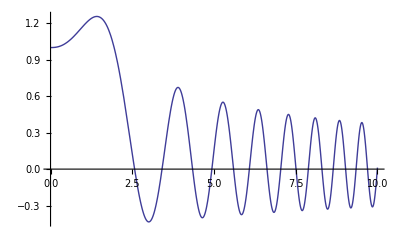

```mathematica
Plot[Fsol[x],{x,0,10}]
```

Just for fun, let's do the other function --- which is just the derivative of F --- too.

```mathematica
Gsol[x_] = Evaluate[G[x]/.Solutionlist]
```

{InterpolatingFunction[{{0.,10.}},<>][x]}

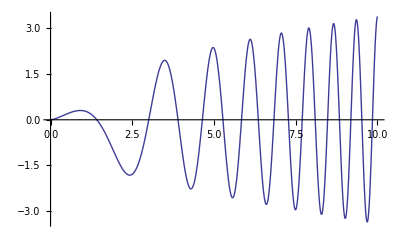

```mathematica
Plot[Gsol[x],{x,0,10}]
```

Note that singular equations can be difficult to handle numerically. If you give Mathematica an equation that is not integrable, you will have problems. 

Another example of a replacement rule. Let’s say you have an expression that you want to evaluate. This can be handy if you do a calculation and you want to impose a constraint on the solution.

```mathematica
expression1 = a*x^2 + b*x + c;
expression2 = expression1/. {a-> 3, b-> -37, c-> -120}
```

3 x^2-37 x-120

```mathematica
We can also do rootfinding in Mathematica. Using the simple example above :
```

```mathematica
FindRoot[expression2,{x,4.0}]
```

{x→-2.66667}

```mathematica
FindRoot[expression2 == 0, {x,4.0}]
```

{x→-2.66667}

```mathematica
We had to tell FindRoot what the independent variable was and give it a starting point. Using x0 = 4 as our starting point, FindRoot only found the nearest root of the equation, x = -8/3. It didn' t find the other root at x = 15. We could also define a function and use FindRoot to find zeros of that function. Let's try a simple example. Note that we are defining H as a function of x, which requires the syntax H[x_] := .
```

```mathematica
H[x_] := x^3 + 16*x + Sin[2*x+5];
FindRoot[H[x],{x,6.0}]
```

{x→0.0574911}

```mathematica
We can also use FindRoot to solve for the inverse of a function. For an invertible function f (x) = y, solve for f^(-1) (y) = x by finding the root of f^(-1)(y) - x = 0.
```

{y$}↦x/.FindRoot[(ⅇ^(3 x)-2)-y$,{x,1}]

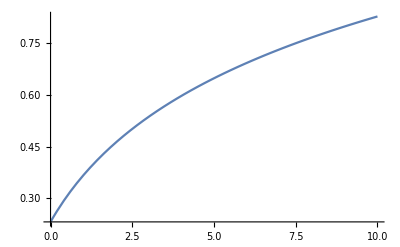

```mathematica
f[x_] := Exp[3*x]-2;
inv[func_,x_] := Function[{y},x/.FindRoot[func-y,{x,1}]];
einv = inv[f[x],x]
Plot[einv[x],{x,0,10}]
```